```mathematica
TwoAxisListLinePlot[{f_,g_}(*,{x_,x1_,x2_}*),p:OptionsPattern[]]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},p]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\CLQ-PI\pi\Desktop\mathematica_drawing_template

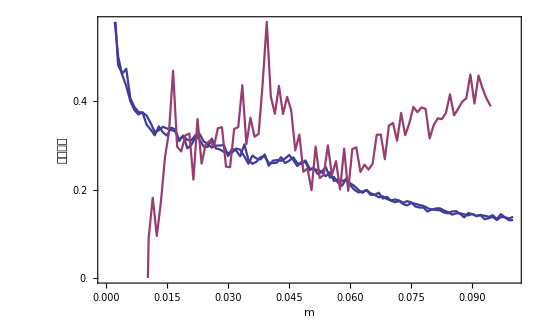

```mathematica
TwoAxisListLinePlot[{
{MapIndexed[{#2[[1]]*0.001,#1["线条密度"]}&,(Get@FileNameJoin[{"测试数据","thedata4.wl"}])],MapIndexed[{#2[[1]]*0.001,#1["线条密度"]}&,(Get@FileNameJoin[{"测试数据","thedata3.wl"}])]},
MovingAverage[{#[[1,1]],((#[[2]]-#[[1]])[[2]]/(#[[2]]-#[[1]])[[1]])}&/@Partition[MapIndexed[{#2[[1]]*0.001,#1["线条密度"]}&,(Get@FileNameJoin[{"测试数据","thedata3.wl"}])],2,1],10]},
FrameLabel->{{"线条密度","灵敏度"},{"m",""}},LabelStyle->Directive[20]]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_},p:OptionsPattern[]]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[Chop[#,10^-5],2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},p]]
```

```mathematica
TwoAxisPlot[{Sin[x],3Cos[x]},{x,0,10.}]
```

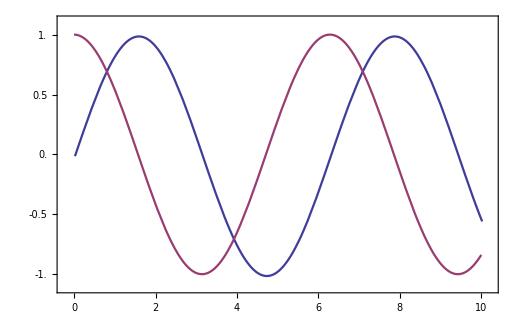

```mathematica
$PlotTheme=""
```

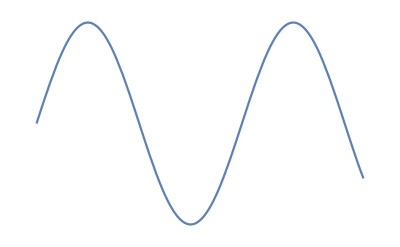

```mathematica
Plot[Sin[x],{x,0,10},PlotTheme->"NoAxes"]
```

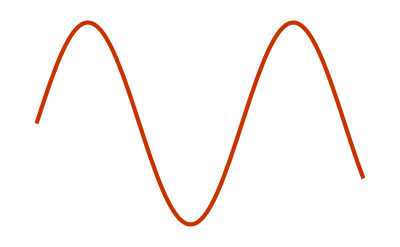

```mathematica
Plot[Sin[x],{x,0,10},PlotTheme->{"Web","NoAxes"}]
```

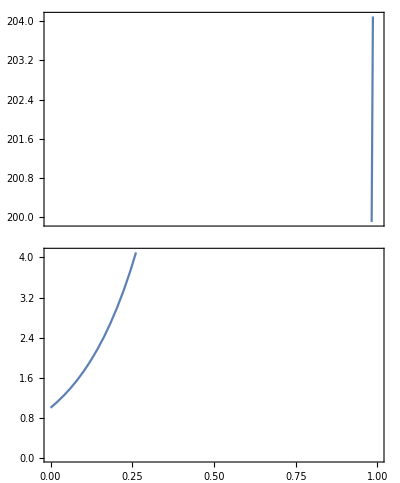

```mathematica
GraphicsGrid[{
 {Plot[220^x,{x,0,1},PlotRange->{{0,1},{200-0.1,204.1}},Axes->False,Frame->True,FrameTicks->{{True,False},{False,False}},FrameStyle->{{Automatic,Automatic},{Directive[(*Thickness[0.02],*)Dashed,Gray],Automatic}},Ticks->{None, Automatic}]},{Plot[220^x,{x,0,1},PlotRange->{{0,1},{0,4.1}},Frame->{{True,True},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->False]}},Spacings->{0,-10}]
```

```mathematica
TwoAxisPlotud[fun_,rangex_,rangey1_,rangey2_,other___]:=GraphicsGrid[{
 {Plot[fun,rangex,PlotRange->{rangex[[2;;-1]],rangey2},Axes->False,Frame->{{True,True},{False,True}},FrameTicks->{{True,False},{False,False}},Ticks->{None, Automatic}]},{Plot[fun,rangex,PlotRange->{rangex[[2;;-1]],rangey1},Frame->{{True,True},{True,True}},
FrameStyle->{{Automatic,Automatic},{Automatic,Directive[Thickness[0.01],Dashed]}},
(*FrameStyle->{{Automatic,Automatic},{Automatic,Directive[Thick,Dashed]}},*)FrameTicks->{{True,False},{True,False}},Axes->False]}},Spacings->{0,-15}]
```

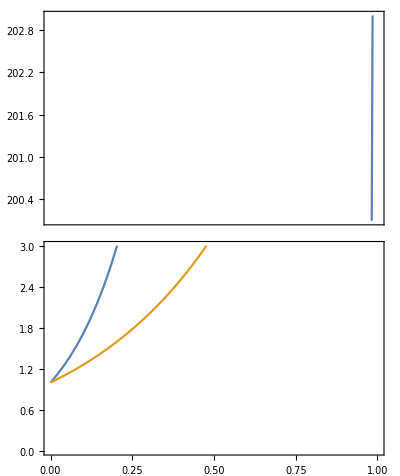

```mathematica
TwoAxisPlotud[{220^x,10^x},{x,0,1},{0,3},{200.1,203}]
```